## Depth prediction models from the reference horizon

### Input set of horizons

```mathematica
set1= {2, {3,1},  {3,4},{3,2},  {3,3}, {4,1},  {4,4},{4,2},  {4,3}}; (*{reference h., {predicted h., method},..., {predicted h., method}}*)
subsets1 = subsets[set1] (*make subsets of horizons for different dMethods*)


(*also you need : wellDataset, reference horizons and time sections (isochrons)! use test.nb from PARAMETRES to WELLS:*)
```

{{2,3,4},{2,3,4},{2,3,4},{2,3,4}}

```mathematica
ref1 =resultHT[[1]]; (*reference horizon = horizon #1 evaluated by HT method (reference - surface) calibrated on wells (!!!exactly it is second horizon!!!)*)
```

```mathematica
ds = wellDataset; (*wellDataset from test.nb*)
timeSection = time; (*timeSection from test.nb*)
```

### Evaluation

```mathematica
Print["_____________dHdT_____________"]
lmSet`dhdt= dHdTMethod2D[subsets1[[1]],ref1, ds, timeSection, dt][["lmSet"]];
result`dhdt= dHdTMethod2D[subsets1[[1]],ref1, ds, timeSection, dt][["fits"]];
plotData`dhdt= dHdTMethod2D[subsets1[[1]],ref1, ds, timeSection, dt][["plotData"]];
rs`dhdt= dHdTMethod2D[subsets1[[1]],ref1, ds, timeSection, dt][["RSquared"]]
fits`dhdt= dHdTMethod2D[subsets1[[1]],ref1, ds, timeSection, dt][["fits"]];
rms`dhdt= dHdTMethod2D[subsets1[[1]],ref1, ds, timeSection, dt][["RMSError"]]
Print["_____________dVdT_____________"]
lmSet`dvdt= dVdTMethod2D[subsets1[[2]],ref1, ds, timeSection, dt][["lmSet"]];
result`dvdt= dVdTMethod2D[subsets1[[2]],ref1, ds, timeSection, dt][["fits"]];
plotData`dvdt= dVdTMethod2D[subsets1[[2]],ref1, ds, timeSection, dt][["plotData"]];
rs`dvdt= dVdTMethod2D[subsets1[[2]],ref1, ds, timeSection, dt][["RSquared"]]
rms`dvdt= dVdTMethod2D[subsets1[[2]],ref1, ds, timeSection, dt][["RMSError"]]
dO`dvdt= dVdTMethod2D[subsets1[[2]],ref1, ds, timeSection, dt][["depthObjective"]]
dPr`dvdt= dVdTMethod2D[subsets1[[2]],ref1, ds, timeSection, dt][["depthPredicted"]]
errors`dvdt= dVdTMethod2D[subsets1[[2]],ref1, ds, timeSection, dt][["errors"]]
positions`dvdt= dVdTMethod2D[subsets1[[2]],ref1, ds, timeSection, dt][["positions"]]
Print["_____________dTdH_____________"]
lmSet`dtdh= dTdHMethod2D[subsets1[[3]],ref1, ds, timeSection, dh][["lmSet"]];
result`dtdh= dTdHMethod2D[subsets1[[3]],ref1, ds, timeSection, dh][["fits"]];
plotData`dtdh= dTdHMethod2D[subsets1[[3]],ref1, ds, timeSection, dh][["plotData"]]; 
rs`dtdh= dTdHMethod2D[subsets1[[3]],ref1, ds, timeSection, dh][["RSquared"]]
rms`dtdh= dTdHMethod2D[subsets1[[3]],ref1, ds, timeSection, dh][["RMSError"]]
Print["_____________dVave_____________"]
result`dvave= dVaveMethod2D[subsets1[[4]],ref1, ds, timeSection][["fits"]];
rms`dvave= dVaveMethod2D[subsets1[[4]],ref1, ds, timeSection][["RMSError"]]
vave`dvave= dVaveMethod2D[subsets1[[4]],ref1, ds, timeSection][["vAveTable"]]
```

_____________dHdT_____________

{0.99925,0.996538}

{6.80903,15.6533}

_____________dVdT_____________

{0.0209988,0.0195946}

{6.90388,15.9882}

{{-2471.33,-1973.33,-2149.33,-2157.33,-1462.33,-1513.33,-1524.33,-2036.33,-1926.33,-1943.33},{-2716.33,-2410.33,-2335.33,-2276.33,-1904.33,-1946.33,-1973.33,-2231.33,-2202.33,-2215.33}}

{{-2473.38,-1966.86,-2155.64,-2168.35,-1460.34,-1507.26,-1512.4,-2042.48,-1927.19,-1943.45},{-2717.39,-2395.96,-2350.2,-2298.7,-1885.03,-1930.98,-1956.42,-2250.5,-2200.49,-2225.66}}

{{2.04196,-6.47079,6.30825,11.0135,-1.99517,-6.07748,-11.9325,6.14829,0.851708,0.112222},{1.05409,-14.3706,14.8658,22.3682,-19.2996,-15.3582,-16.912,19.1634,-1.83926,10.3282}}

{200,1300,1600,1800,3500,3700,3800,5200,7900,8200}

_____________dTdH_____________

{0.99925,0.996538}

{6.81159,15.6805}

_____________dVave_____________

{6.81398,15.6704}

{2414.02,2472.96}

```mathematica
vaveDs = Dataset[<|Table[<|StringJoin["Гор-нт ",ToString[i]]-><|StringJoin["Средняя ","скорость, ", "м/c"] ->IntegerPart[vave`dvave[[i]]]|>|>, {i, 2}]|>]
```

```mathematica
datasetS = Dataset[<|Table[<|StringJoin["Гор-нт ",ToString[i]]-><|"RMS HT, м" ->SetPrecision[rms`dhdt[[i]],6], "RMS Средняя ск-сть, м" -> SetPrecision[rms`dvave[[i]],6],"RMS VT, м" -> SetPrecision[rms`dvdt[[i]],6]," RMS TH, м" ->  SetPrecision[rms`dtdh[[i]],6]|>|>, {i, 2}]|>]
```

### Linear regression plots

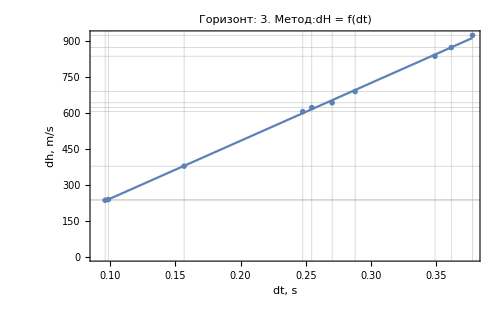
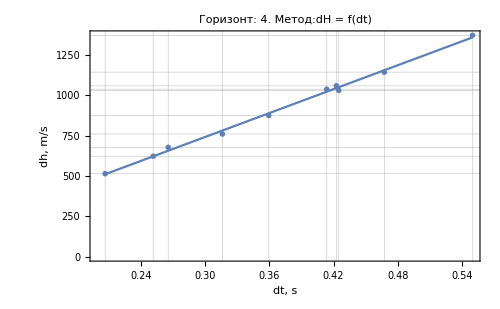

```mathematica
LinearRegressionPlots[plotData`dhdt,lmSet`dhdt, dt, "dH = f(dt)", {"dt, s","dh, m/s"}]
```

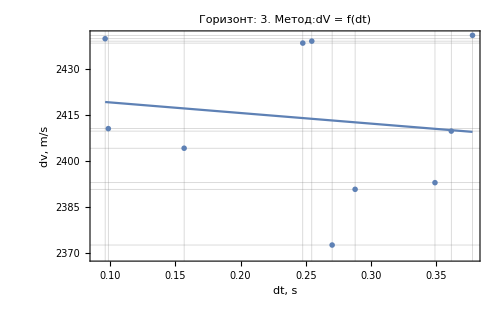
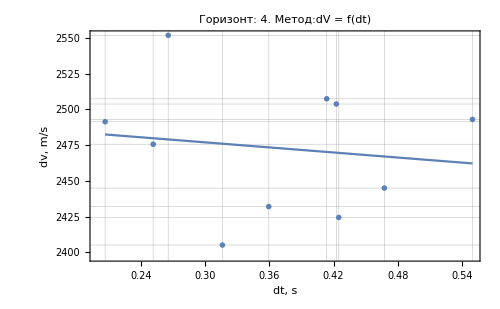

```mathematica
LinearRegressionPlots[plotData`dvdt[[All,All, 2;;3]],lmSet`dvdt, dt, "dV = f(dt)", {"dt, s","dv, m/s"}]
```

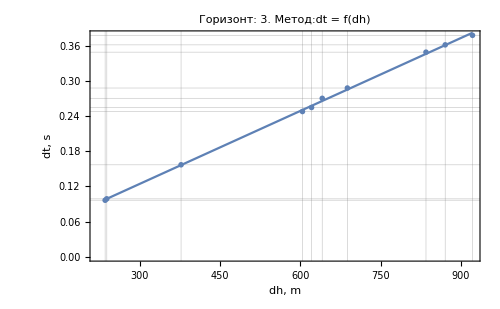
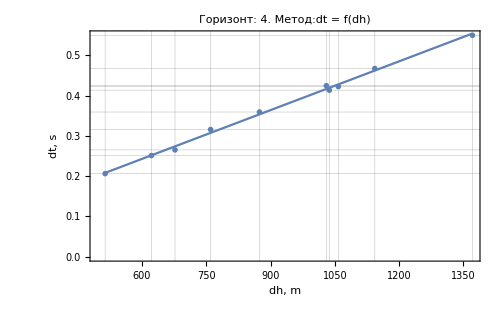

```mathematica
LinearRegressionPlots[plotData`dtdh,lmSet`dtdh, dh, "dt = f(dh)", {"dh, m", "dt, s"}]
```

## Result

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	
ListLinePlot[result`dhdt, PlotStyle->{Blue}],
	ListLinePlot[result`dvdt, PlotStyle->{Red}],
	ListLinePlot[result`dtdh, PlotStyle->{Green}],
ListLinePlot[result`dvave, PlotStyle->{Yellow}]
]
```

-Graphics-

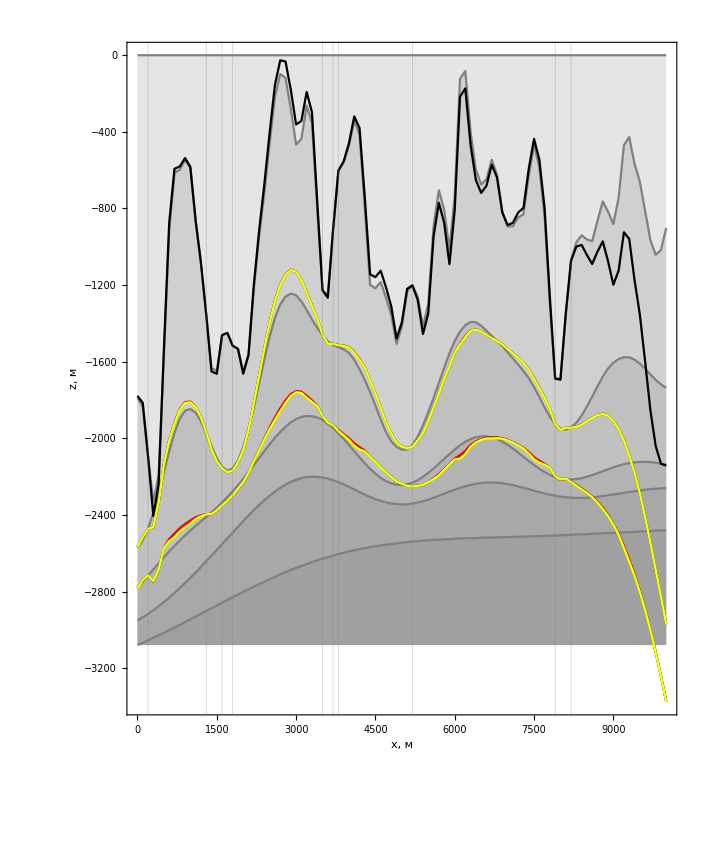

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]]},Filling -> Bottom,  PlotStyle->Gray],
ListLinePlot[ref1, PlotStyle->{Black}, ImageSize -> 500],	
ListLinePlot[result`dhdt, PlotStyle->{Blue}], 
	ListLinePlot[result`dvdt, PlotStyle->{Red}],
	ListLinePlot[result`dtdh, PlotStyle->{Green}],
ListLinePlot[result`dvave, PlotStyle->{Yellow} ], PlotRange->All, Frame -> True, PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.02], Scaled[0.02]}},FrameLabel->{"x, м", "z, м"}, FrameStyle -> Directive[16, Black], AspectRatio->1.2
]
```

### Input set of horizons

```mathematica
set2= {3, {4,1},  {4,4},{4,2},  {4,3}}; (*{reference h., {predicted h., method},..., {predicted h., method}}*)
subsets2 = subsets[set2] (*make subsets of horizons for different dMethods*)


(*also you need : wellDataset, reference horizons and time sections (isochrons)! use test.nb from PARAMETRES to WELLS:*)
```

{{3,4},{3,4},{3,4},{3,4}}

```mathematica
ref2 =result`dvdt[[1]] ;(*reference horizon = horizon #1 evaluated by HT method (reference - surface) calibrated on wells (!!!exactly it is second horizon!!!)*)
```

```mathematica
ds = wellDataset; (*wellDataset from test.nb*)
timeSection = time; (*timeSection from test.nb*)
```

```mathematica
Print["_____________dHdT_____________"]
lmSet1`dhdt= dHdTMethod2D[subsets2[[1]],ref2, ds, timeSection, dt][["lmSet"]];
result1`dhdt= dHdTMethod2D[subsets2[[1]],ref2, ds, timeSection, dt][["fits"]];
plotData1`dhdt= dHdTMethod2D[subsets2[[1]],ref2, ds, timeSection, dt][["plotData"]];
rs1`dhdt= dHdTMethod2D[subsets2[[1]],ref2, ds, timeSection, dt][["RSquared"]]
fits1`dhdt= dHdTMethod2D[subsets2[[1]],ref2, ds, timeSection, dt][["fits"]];
rms1`dhdt= dHdTMethod2D[subsets2[[1]],ref2, ds, timeSection, dt][["RMSError"]]
Print["_____________dVdT_____________"]
lmSet1`dvdt= dVdTMethod2D[subsets2[[2]],ref2, ds, timeSection, dt][["lmSet"]];
result1`dvdt= dVdTMethod2D[subsets2[[2]],ref2, ds, timeSection, dt][["fits"]];
plotData1`dvdt= dVdTMethod2D[subsets2[[2]],ref2, ds, timeSection, dt][["plotData"]];
rs1`dvdt= dVdTMethod2D[subsets2[[2]],ref2, ds, timeSection, dt][["RSquared"]]
rms1`dvdt= dVdTMethod2D[subsets2[[2]],ref2, ds, timeSection, dt][["RMSError"]]
dO1`dvdt= dVdTMethod2D[subsets2[[2]],ref2, ds, timeSection, dt][["depthObjective"]]
dPr1`dvdt= dVdTMethod2D[subsets2[[2]],ref2, ds, timeSection, dt][["depthPredicted"]]
errors1`dvdt= dVdTMethod2D[subsets2[[2]],ref2, ds, timeSection, dt][["errors"]]
positions1`dvdt= dVdTMethod2D[subsets2[[2]],ref2, ds, timeSection, dt][["positions"]]
Print["_____________dTdH_____________"]
lmSet1`dtdh= dTdHMethod2D[subsets2[[3]],ref2, ds, timeSection, dh][["lmSet"]];
result1`dtdh= dTdHMethod2D[subsets2[[3]],ref2, ds, timeSection, dh][["fits"]];
plotData1`dtdh= dTdHMethod2D[subsets2[[3]],ref2, ds, timeSection, dh][["plotData"]]; 
rs1`dtdh= dTdHMethod2D[subsets2[[3]],ref2, ds, timeSection, dh][["RSquared"]]
rms1`dtdh= dTdHMethod2D[subsets2[[3]],ref2, ds, timeSection, dh][["RMSError"]]
Print["_____________dVave_____________"]
result1`dvave= dVaveMethod2D[subsets2[[4]],ref2, ds, timeSection][["fits"]];
rms1`dvave= dVaveMethod2D[subsets2[[4]],ref2, ds, timeSection][["RMSError"]]
vave1`dvave= dVaveMethod2D[subsets2[[4]],ref2, ds, timeSection][["vAveTable"]]
```

_____________dHdT_____________

{0.999785}

{6.89072}

_____________dVdT_____________

{0.260704}

{7.23194}

{{-2716.33,-2410.33,-2335.33,-2276.33,-1904.33,-1946.33,-1973.33,-2231.33,-2202.33,-2215.33}}

{{-2717.76,-2404.05,-2340.56,-2286.43,-1900.2,-1938.94,-1960.86,-2238.58,-2205.85,-2218.12}}

{{1.42391,-6.28576,5.22648,10.0921,-4.1303,-7.39461,-12.4769,7.24273,3.52018,2.78217}}

{200,1300,1600,1800,3500,3700,3800,5200,7900,8200}

_____________dTdH_____________

{0.999785}

{6.86557}

_____________dVave_____________

{8.33107}

{2592.32}

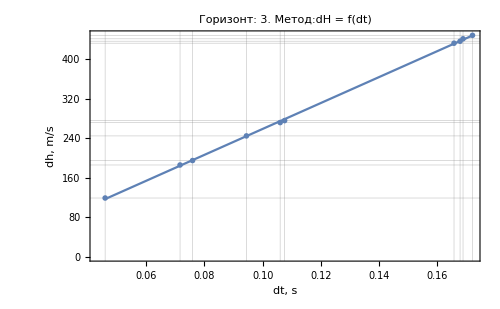

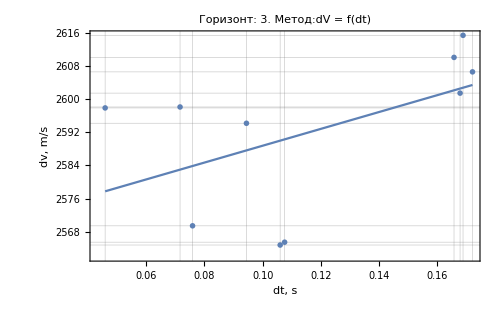

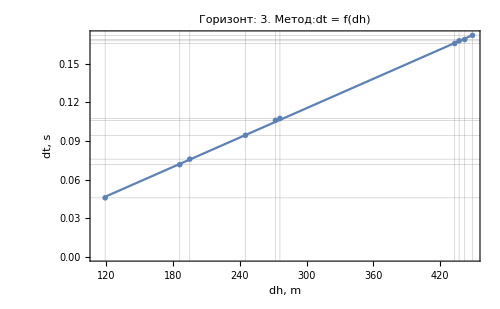

```mathematica
LinearRegressionPlots[plotData1`dhdt,lmSet1`dhdt, dt, "dH = f(dt)", {"dt, s","dh, m/s"}]
LinearRegressionPlots[plotData1`dvdt[[All,All, 2;;3]],lmSet1`dvdt, dt, "dV = f(dt)", {"dt, s","dv, m/s"}]
LinearRegressionPlots[plotData1`dtdh,lmSet1`dtdh, dh, "dt = f(dh)", {"dh, m", "dt, s"}]
```

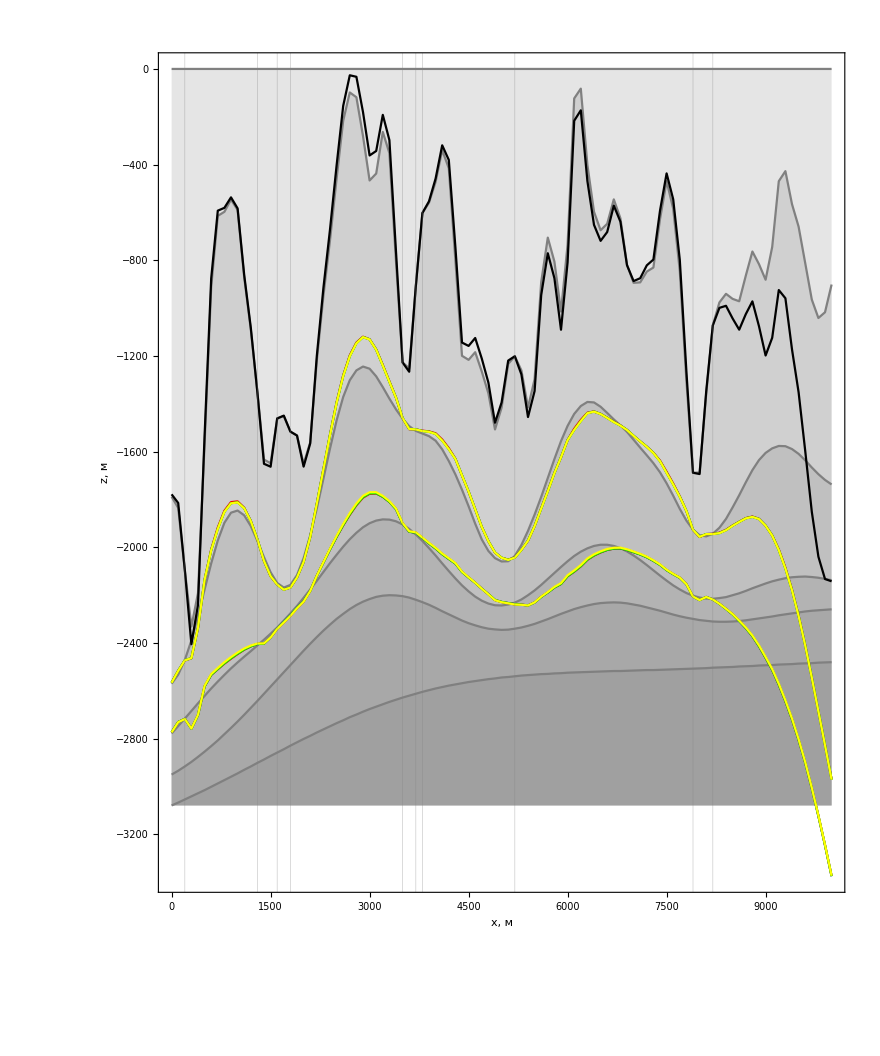

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]]},Filling -> Bottom,  PlotStyle->Gray],
ListLinePlot[ref1, PlotStyle->{Black}, ImageSize -> 500],	
ListLinePlot[result`dhdt[[1]], PlotStyle->{Blue}], 
	ListLinePlot[result`dvdt[[1]], PlotStyle->{Red}],
	ListLinePlot[result`dtdh[[1]], PlotStyle->{Green}],
ListLinePlot[result`dvave[[1]], PlotStyle->{Yellow} ],
ListLinePlot[result1`dhdt, PlotStyle->{Blue}], 
	ListLinePlot[result1`dvdt, PlotStyle->{Red}],
	ListLinePlot[result1`dtdh, PlotStyle->{Green}],
ListLinePlot[result1`dvave, PlotStyle->{Yellow} ], PlotRange->Full, Frame -> True, PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.02], Scaled[0.02]}},FrameLabel->{"x, м", "z, м"}, FrameStyle -> Directive[16, Black], AspectRatio->1.2
]
```

```mathematica
rms1`dhdt
```

{6.89072}

```mathematica
datasetS = Dataset[<|"Прогнозный"-><|Table[<|StringJoin["Гор-нт ",ToString[i+2]]-><|"RMS HT, м" ->SetPrecision[rms`dhdt[[i]],3], "RMS Средняя ск-сть, м" -> SetPrecision[rms`dvave[[i]],3],"RMS VT, м" -> SetPrecision[rms`dvdt[[i]],3]," RMS TH, м" ->  SetPrecision[rms`dtdh[[i]],3]|>|>, {i, 2}]|>|>]
```

```mathematica
ds = Join[datasetS,datasetS1]
```

```mathematica
ds
```

```mathematica
datasetS1 = Dataset[<|"от гор-та 3"-><|Table[<|StringJoin["Гор-нт ",ToString[i+3]]-><|"RMS HT, м" ->SetPrecision[rms1`dhdt[[i]],3], "RMS Средняя ск-сть, м" -> SetPrecision[rms1`dvave[[i]],3],"RMS VT, м" -> SetPrecision[rms1`dvdt[[i]],3]," RMS TH, м" ->  SetPrecision[rms1`dtdh[[i]],3]|>|>, {i, 2}]|>|>]
```

Part::partw: Part 2 of {6.89072} does not exist.

Part::partw: Part 2 of {8.33107} does not exist.

Part::partw: Part 2 of {7.23194} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

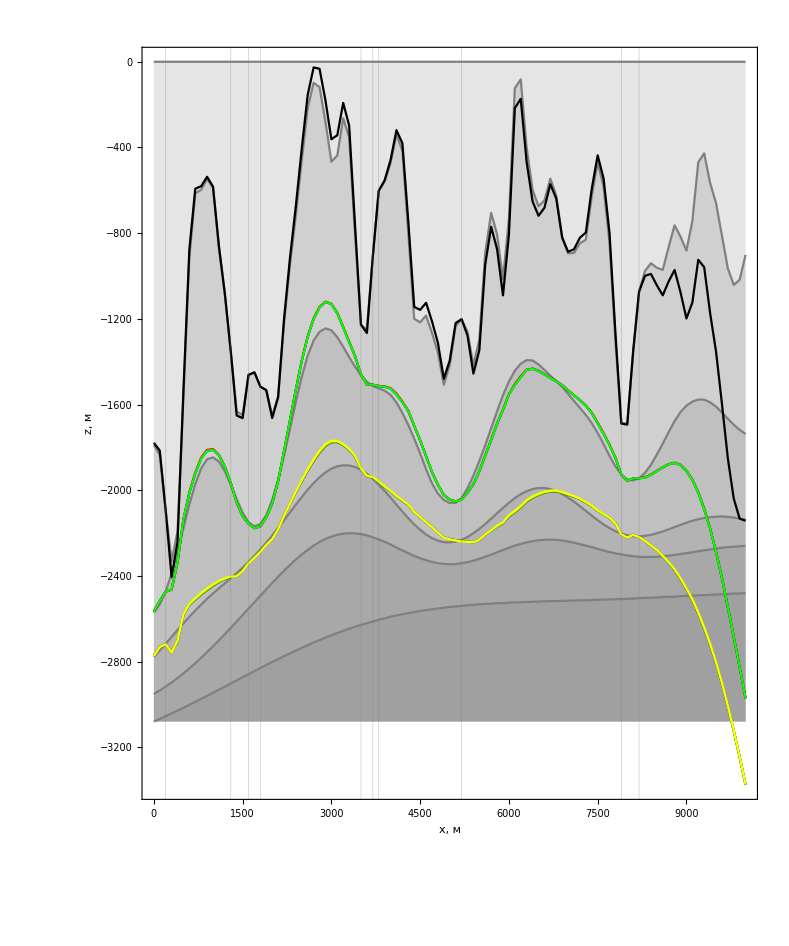

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]]},Filling -> Bottom,  PlotStyle->Gray],
ListLinePlot[ref1, PlotStyle->{Black}, ImageSize -> 500],	
ListLinePlot[result`dhdt[[1]], PlotStyle->{Blue}], 
	ListLinePlot[result`dvdt[[1]], PlotStyle->{Red}],
	ListLinePlot[result`dtdh[[1]], PlotStyle->{Green}],
ListLinePlot[result1`dvave[[1]], PlotStyle->{Yellow} ],
ListLinePlot[result1`dhdt, PlotStyle->{Blue}], 
	ListLinePlot[result1`dvdt, PlotStyle->{Red}],
	ListLinePlot[result1`dtdh, PlotStyle->{Green}],
ListLinePlot[result1`dvave, PlotStyle->{Yellow} ], PlotRange->All, Frame -> True, PlotRangePadding -> {{Scaled[0.02], Scaled[0.02]}, {Scaled[0.02], Scaled[0.02]}},FrameLabel->{"x, м", "z, м"}, FrameStyle -> Directive[16, Black], AspectRatio->1.2
]
```